# 2D Graphics

Lesson: 2D Graphics - Primitives & Directives
Course: Mathematica Essentials

## Introduction

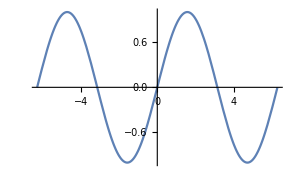

```mathematica
Plot[Sin[x],{x,-2Pi,2Pi}]
```

```mathematica
Plot3D[Exp[Sin[0.5x y]],{x,-3,3},{y,-3,3}]
```

-Graphics3D-

```mathematica
DiscretePlot3D[Sin[x √y],{x,-20,20},
		{y,0,40},ExtentSize->Full]
```

-Graphics3D-

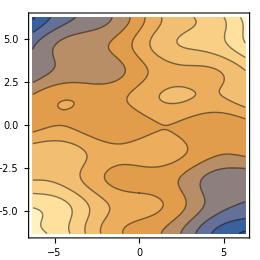

```mathematica
ContourPlot[Sin[x]-Cos[2y]+0.3x y,
		{x,-2Pi,2Pi},{y,-2Pi,2Pi}]
```

## Graphics Primitives

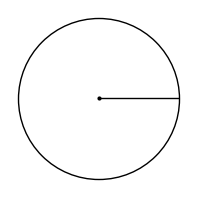

```mathematica
Graphics[{   Circle[{0,0},1],   Line[{{0,0},{1,0}}],   Point[{0,0}]   }]
```

```mathematica
circles=Table[Circle[{0,0},r],{r,0,1,0.1}];
Graphics[circles]
```

-Graphics-

```mathematica
circles
```

{Circle[{0,0},0.],Circle[{0,0},0.1],Circle[{0,0},0.2],Circle[{0,0},0.3],Circle[{0,0},0.4],Circle[{0,0},0.5],Circle[{0,0},0.6],Circle[{0,0},0.7],Circle[{0,0},0.8],Circle[{0,0},0.9],Circle[{0,0},1.]}

## Lines

```mathematica
Graphics[{ Line[{{0,0},{1,1}}] }]
```

-Graphics-

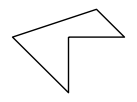

```mathematica
Graphics[{ Line[{{0,0},{1,0},{1/2,1/2},{-1,0},{0,-1},{0,0}}]}]
```

```mathematica
pts=Table[{x,Sin[x]},{x,-2Pi,2Pi,0.1}];
Length[pts]
```

126

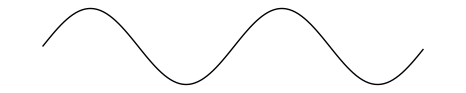

```mathematica
Graphics[Line[pts]]
```

## Filled Shapes

```mathematica
Graphics[{
Circle[{0,0},1],Line[{{0,0}, {1,0},{0,1},{0,0}}]
}]
```

-Graphics-

```mathematica
Graphics[{
Disk[{0,0},1]
}]
```

-Graphics-

```mathematica
Graphics[{
Polygon[{{0,0}, {1,0},{0,1},{0,0}}]
}]
```

-Graphics-

## Directives

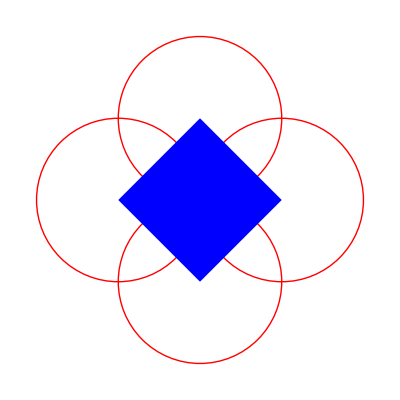

```mathematica
Graphics[{
Red,
Circle[{1,0},1], Circle[{0,1},1], Circle[{-1,0},1], Circle[{0,-1},1],
Blue,
Polygon[{{1,0},{0,1},{-1,0},{0,-1}}],
}]
```

```mathematica
FullForm[Red]
```

RGBColor[1,0,0]

```mathematica
FullForm[Blue]
```

RGBColor[0,0,1]

## Thickness

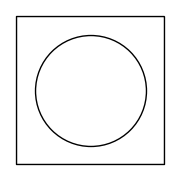

```mathematica
shape=Graphics[{
Thin,
Circle[{0,0},1.5],
Thick,
Line[{{2,2}, {-2,2}, {-2,-2}, {2,-2}, {2,2}}]
}]
```

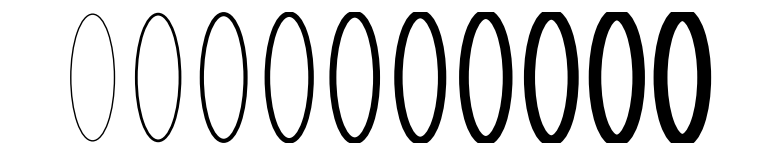

```mathematica
circles=Table[{AbsoluteThickness[i],Circle[{3i,0},1]},{i,1,10}];
Graphics[circles]
```

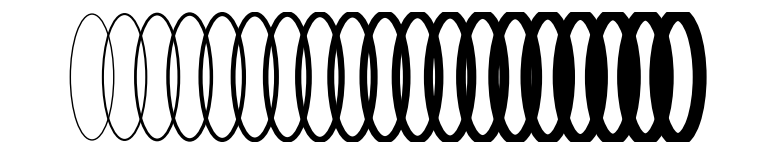

```mathematica
circles=Table[{AbsoluteThickness[i],Circle[{3i,0},1]},{i,1,10,0.5}];
Graphics[circles]
```

## Edge Directives

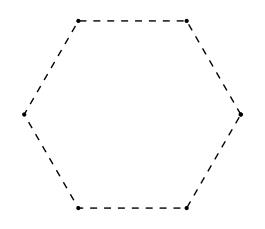

```mathematica
pts=Table[{Cos[θ],Sin[θ]},{θ,0,2π,2π/6}];
Graphics[{
Dashed,Thick,Line[pts],Point[pts]
}]
```

## 08 - Point Directives

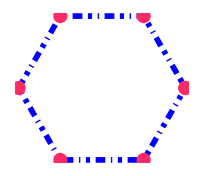

```mathematica
pts=Table[{Cos[θ],Sin[θ]},{θ,0,2π,2π/6}];
Graphics[{
Thickness[0.02],Blue,AbsoluteDashing[{1,4, 3,4,7,4}],Line[pts],
PointSize[0.05],RGBColor[1,0.17,0.4],Point[pts]
}]
```